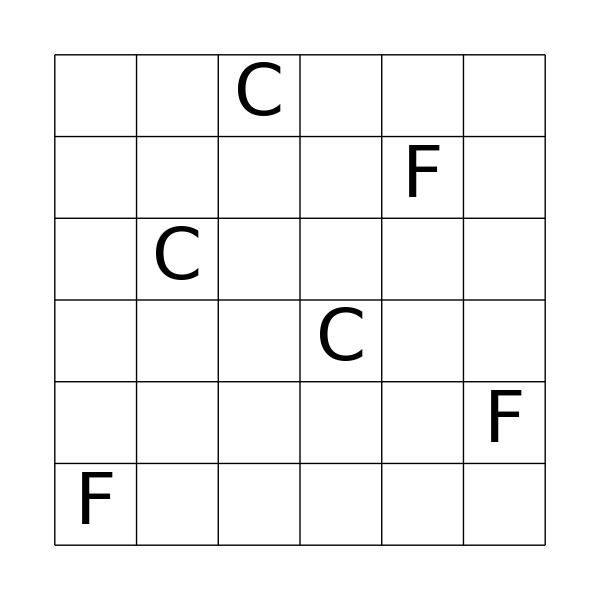

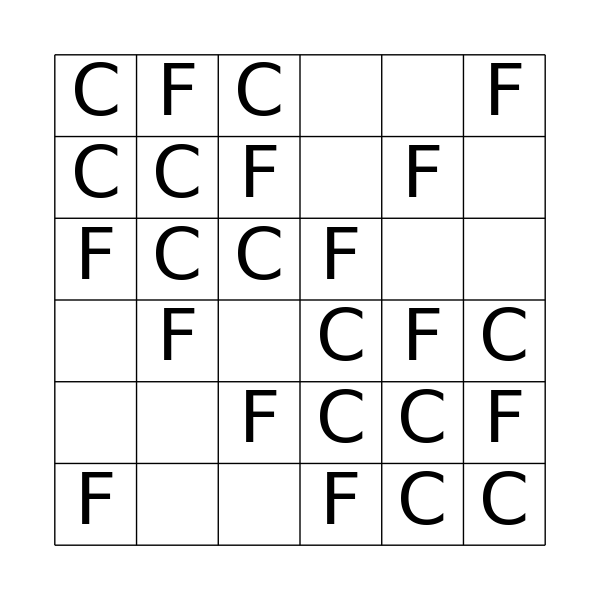

-Graphics-

-Graphics-

```mathematica
arith=Flatten[Table[{i,i+j,i+2j},{i,0,7},{j,1,(9-i)/2}],1];
(* arithmetic sequence *)
```

```mathematica
arith=Select[Flatten[Table[{i,i+j,j},{i,1,9},{j,1,9}],1],#[[2]]≤9&];
(* ends adding to middle *)
```

```mathematica
f[n_]:=Flatten[Table[{i,j,k},{i,1,n-2},{j,i+1,n-1},{k,j+1,n}],2]
```

```mathematica
g[a_,b_]:=ReplacePart[ReplacePart[ReplacePart[Table[-1,{n}],a[[1]]->b[[1]]],a[[2]]->b[[2]]],a[[3]]->b[[3]]]
```

```mathematica
checkrow[L_]:=Module[{LL},
LL=Select[L,#≥0&];
If[(Union[LL]=!=LL)||(Length[LL]>3),Return[False]];
(Length[LL]<3)||(MemberQ[arith,LL])]
(* arithmetic sequences *)
```

```mathematica
checkrow[L_]:=Module[{LL},
LL=Select[L,#≥0&];
If[(Length[LL]>3),Return[False]];
If[Length[LL]==2&&LL[[1]]≥LL[[2]],Return[False]];
(Length[LL]<3)||(MemberQ[arith,LL])]
(* ends adding to middle *)
```

```mathematica
checkmatrix[L_]:=Apply[And,Map[checkrow,L]]~And~Apply[And,Map[checkrow,Transpose[L]]]
```

```mathematica
rp:=Transpose[Sort[Table[{Random[],i},{i,1,n}]]][[2]]
```

```mathematica
initialize:=Module[{A,i},
A=Table[-1,{n},{n}];
r=rp;
For[i=1,i≤n,i++,
A=ReplacePart[A,{i,r[[i]]}->RandomInteger[{0,9}]]];A]
```

```mathematica
beforepic[show_]:=Style[Graphics[{
Table[Line[{{0,-i},{n,-i}}],{i,0,n}],Table[Line[{{i,0},{i,-n}}],{i,0,n}],
MapIndexed[If[#1≥0,Text[Style[#1,FontSize->16],{#2[[1]]-1/2,1/2-#2[[2]]}],{}]&,show,{2}]
},ImageSize->20n],Antialiasing->False]
```

```mathematica
n=8;
poss=Flatten[Outer[g,f[n],arith,1],1];
Length[poss]
```

2016

```mathematica
For[k=1,k>0,k++,
start=initialize;
stac={start};
solns={};
While[Length[stac]>0&&Length[solns]<2,
cur=First[stac];
stac=Rest[stac];
If[Length[Select[Flatten[cur],#≥0&]]==3n,AppendTo[solns,cur],
ct=1;
While[Length[Select[cur[[ct]],#≥0&]]==3,ct++];
pos=Flatten[Position[cur[[ct]],x_?(#≥0&)]][[1]];
newrows=Select[poss,#[[pos]]==cur[[ct,pos]]&];
possmatrices=Map[ReplacePart[cur,ct->#]&,newrows];
newmatrices=Select[possmatrices,checkmatrix];
stac=Join[newmatrices,stac];
]];
If[Length[solns]==1,Print[beforepic[start]];Print[beforepic[solns[[1]]]]]]
```

-Graphics-

```mathematica
rp:=Transpose[Sort[Table[{Random[],i},{i,1,n}]]][[2]]
```

```mathematica
beforepic[show_]:=Graphics[{
Table[Line[{{0,-i},{n,-i}}],{i,0,n}],Table[Line[{{i,0},{i,-n}}],{i,0,n}],
MapIndexed[If[#1=!=-1,Text[Style[#1,FontSize->14,FontColor->Which[#1=="C",Blue,True,Red]],{#2[[1]]-1/2,.45-#2[[2]]}],{}]&,show,{2}]
},ImageSize->18n]
```

```mathematica
initialize:=Module[{A,i},
A=Table[-1,{n},{n}];
r=rp;
For[i=1,i≤n,i++,
A=ReplacePart[A,{i,r[[i]]}->{"C","F"}[[RandomInteger[{1,2}]]]]];A]
```

```mathematica
beforepic[start]
```

-Graphics-

```mathematica
checkrow[L_]:=Module[{LL},
LL=Select[L,#=!=-1&];
If[(Count[L,"C"]>2)||(Count[L,"F"]>2)||(Count[L,""]>n-3),Return[False]];
If[(Count[L,"F"]==2),If[Abs[Apply[Subtract,Flatten[Position[L,"F"]]]]==1,Return[False]]];
If[(Count[L,"C"]==2),If[Abs[Apply[Subtract,Flatten[Position[L,"C"]]]]>n-3,Return[False]]];
If[(Count[L,"C"]==2)&&(Count[L,"F"]==2)&&(Count[L,""]==n-4)&&Not[MemberQ[poss,L]],Return[False]];
True]
(* CF *)
```

```mathematica
checkmatrix[L_]:=Apply[And,Map[checkrow,L]]~And~Apply[And,Map[checkrow,Transpose[L]]]
```

```mathematica
n=6;poss=Select[Permutations[{"C","C","F","F"}~Join~Table["",{n-4}]],Abs[Apply[Subtract,Flatten[Position[#,"C"]]]]<Abs[Apply[Subtract,Flatten[Position[#,"F"]]]]&];
Length[poss]
```

31

```mathematica
For[k=1,k>0,k++,
p=0;
start=initialize;
stac={start};
solns={};
While[Length[stac]>0&&Length[solns]<2,
cur=First[stac];
stac=Rest[stac];
If[Length[Select[Flatten[cur],#=!=-1&]]==n^2,AppendTo[solns,cur],
ct=1;
While[Length[Select[cur[[ct]],#=!=-1&]]==n,ct++];
pos=Flatten[Position[cur[[ct]],x_?(MemberQ[{"C","F",""},#]&)]][[1]];
newrows=Select[poss,#[[pos]]==cur[[ct,pos]]&];
possmatrices=Map[ReplacePart[cur,ct->#]&,newrows];
newmatrices=Select[possmatrices,checkmatrix];
stac=Join[newmatrices,stac];
]];
If[Length[solns]==1,Print[beforepic[start]];Print[beforepic[solns[[1]]]]]]
```

## 6x6 CF

-Graphics-

-Graphics-

-Graphics-

«495 more identical outputs»

## 7x7 CF

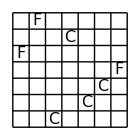

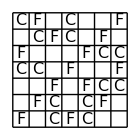

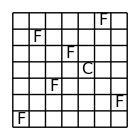

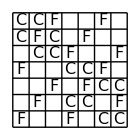

## 4x4 arith

-Graphics-

-Graphics-

-Graphics-

«379 more identical outputs»

## 5x5 arith

-Graphics-

-Graphics-

-Graphics-

«167 more identical outputs»

## 6x6 arith

-Graphics-

-Graphics-

-Graphics-

«465 more identical outputs»

## 7x7 arith

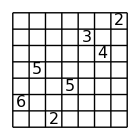

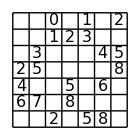

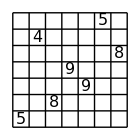

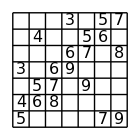

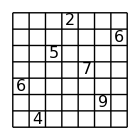

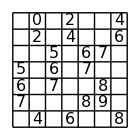

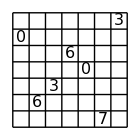

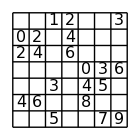

## 4x4 sum

-Graphics-

-Graphics-

-Graphics-

«227 more identical outputs»

## 5x5 sum

-Graphics-

-Graphics-

-Graphics-

«75 more identical outputs»

## 6x6 sum

-Graphics-

-Graphics-

-Graphics-

«83 more identical outputs»

## 7x7 sum

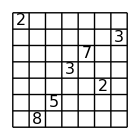

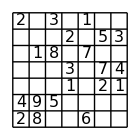

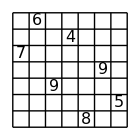

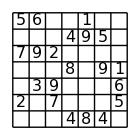

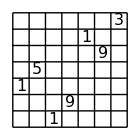

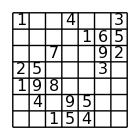

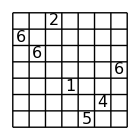

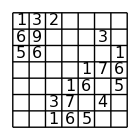

## 8x8 sum